## Решения

```mathematica
Functions[variant_]:= If[variant == 20,
Return@{6 x^2 - 7 y^2 - 65,13 x y + 41 },
Return@{x^2 * ((x+11)^2 + 2 y^2) - 78 y^2, 2 x^2 + 3/2 y^2 - 14}
];
```

```mathematica
F = Functions[23];
```

```mathematica
dF = {D[F, {x, 1}], D[F, {y, 1}]};
```

```mathematica
F // MatrixForm
```

(-78 y^2+x^2 ((11+x)^2+2 y^2)
-14+2 x^2+(3 y^2)/2)

```mathematica
dF // MatrixForm
```

(2 x^2 (11+x)+2 x ((11+x)^2+2 y^2) | 4 x
-156 y+4 x^2 y | 3 y)

```mathematica
Solve[F[[1]] == 0 && F[[2]] == 0, {x, y}, Reals] // N
```

{{x→-1.93255,y→-2.08654},{x→-1.93255,y→2.08654},{x→1.6269,y→-2.4092},{x→1.6269,y→2.4092}}

```mathematica
Plot3D[{F[[1]],F[[2]]},{x,-100,100},{y,-100,100}]
```

-Graphics3D-

## Область сходимости

```mathematica
SetDirectory[NotebookDirectory[]]
data = Import["convergeArea.dat"];
```

D:\BMSTU_coopmode_labs\Numerical methods\Lab5\data

```mathematica
ListContourPlot[data,ClippingStyle->Red,ColorFunction-> "Rainbow"]
```

-Graphics-

```mathematica
func[x_]:=Sin[(√13 x^3-9x-5-√17)/10]+Tan[(x^2+x+2^(1/3))/(3x-5)]+0.6
```

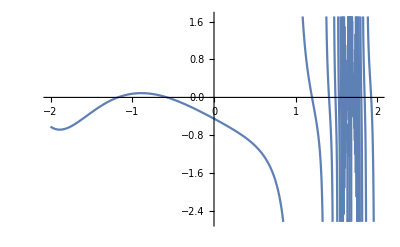

```mathematica
Plot[func[x],{x,-2,2}]
```

```mathematica
func[-1]
```

0.076909

```mathematica
func[0.8]
```

-2.08994